```mathematica
$Assumptions=σ>0
ψ[r_]:=1/(√π σ)*Exp[-r^2/(2 σ^2)]*{1,0}
```

σ>0

```mathematica
2π Integrate[ψ[r].ψ[r]r,{r,0,∞}]
(*Solve[%%==1,NN]*)
```

1

```mathematica
2π Integrate[ψ[r].ψ[r] r^3,{r,0,∞}] (* <ψ|r^2|ψ> *)
```

σ^2

```mathematica
FourierTransform[1/(√π σ)*Exp[(-(x^2+y^2))/(2 σ^2)],{x,y},{kx,ky}]
```

ConditionalExpression[(ⅇ^(-1/2 (kx^2+ky^2) σ^2) σ)/(√π),√(kx^2+ky^2)≥0]

```mathematica
ψ[kx_,ky_]:=(2π)(ⅇ^(-1/2 (kx^2+ky^2) σ^2) σ)/(√π){1,0}
```

```mathematica
Integrate[ψ[kx,ky].ψ[kx,ky],{kx,-∞,∞},{ky,-∞,∞}]/(2π)^2
```

1

```mathematica
H={{0,kx-ⅈ ky},{kx+ⅈ ky,0}}
```

{{0,kx-ⅈ ky},{kx+ⅈ ky,0}}

```mathematica
U=MatrixExp[-ⅈ H t]//FullSimplify
```

{{Cos[√(kx^2+ky^2) t],((-ⅈ kx-ky) Sin[√(kx^2+ky^2) t])/(√(kx^2+ky^2))},{((-ⅈ kx+ky) Sin[√(kx^2+ky^2) t])/(√(kx^2+ky^2)),Cos[√(kx^2+ky^2) t]}}

```mathematica
d2ψ=D[U.ψ[kx,ky],{kx,2}]+D[U.ψ[kx,ky],{ky,2}]//FullSimplify
```

{1/(√(kx^2+ky^2))2 ⅇ^(-1/2 (kx^2+ky^2) σ^2) √π σ (√(kx^2+ky^2) (-t^2-2 σ^2+(kx^2+ky^2) σ^4) Cos[√(kx^2+ky^2) t]+t (-1+2 (kx^2+ky^2) σ^2) Sin[√(kx^2+ky^2) t]),-1/((ⅈ kx+ky) √(kx^2+ky^2))2 ⅇ^(-1/2 (kx^2+ky^2) σ^2) √π σ (√(kx^2+ky^2) t (-1+2 (kx^2+ky^2) σ^2) Cos[√(kx^2+ky^2) t]+(1-(kx^2+ky^2) (-t^2-2 σ^2+(kx^2+ky^2) σ^4)) Sin[√(kx^2+ky^2) t])}

```mathematica
integrand=-ComplexExpand[Conjugate[U.ψ[kx,ky]]].d2ψ//Simplify
```

-1/(kx^2+ky^2)2 ⅇ^(-(kx^2+ky^2) σ^2) π σ^2 (-1-2 ky^2 t^2-4 ky^2 σ^2+2 kx^4 σ^4+2 ky^4 σ^4-2 kx^2 (t^2+2 σ^2-2 ky^2 σ^4)+Cos[2 √(kx^2+ky^2) t])

```mathematica
kintegrand=integrand/.{kx->k Cos[θ], ky-> k Sin[θ]}//FullSimplify
```

-(2 ⅇ^(-k^2 σ^2) π σ^2 (-1+2 k^4 σ^4-2 k^2 (t^2+2 σ^2)+Cos[2 k t]))/k^2

```mathematica
result=Integrate[kintegrand*k,{k,0,∞}]/(2π)
```

t^2+σ^2+t^2 HypergeometricPFQ[{1,1},{3/2,2},-t^2/σ^2]

```mathematica
Series[t^2 HypergeometricPFQ[{1,1},{3/2,2},-t^2/σ^2],{t,∞,3}]//Simplify
```

ⅇ^(-t^2/σ^2+O[1/t]^6) ((ⅈ √π σ^3)/(2 t)-(ⅈ √π σ^5)/(4 t^3)+O[1/t]^4)+(1/2 σ^2 (Log[t^2/σ^2]-PolyGamma[0,1/2])-σ^4/(4 t^2)+O[1/t]^4)

```mathematica
Series[result,{t,0,4}]//Simplify
```

σ^2+2 t^2-t^4/(3 σ^2)+O[t]^5

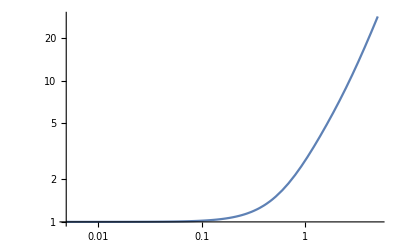

```mathematica
LogLogPlot[result/.{σ->1},{t,0,5}]
```